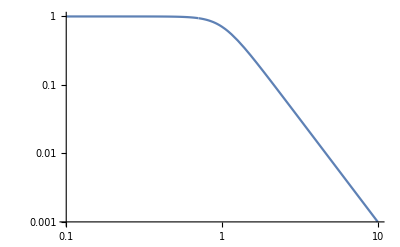

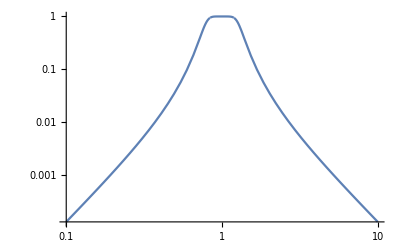

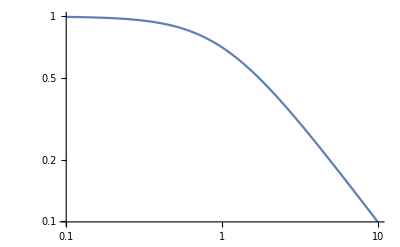

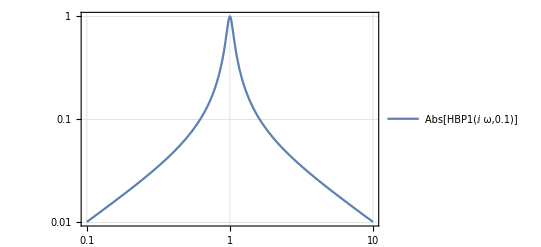

1/(17.+8./s^3+8./s^2+28./s+28. s+8. s^2+8. s^3)

1/(1+10./s+10. s)

```mathematica
HLP[s_]:=1/(s^3+2 s^2+2s+1);
HLP1[s_]:=1/(s+1);
HBP[s_,Δω_]:=HLP[1/Δω(s+1/s)];
HBP1[s_,Δω_]:=HLP1[1/Δω(s+1/s)];
LogLogPlot[Abs[HLP[ⅈ ω]],{ω,0.1,10}]
LogLogPlot[Abs[HBP[ⅈ ω,0.5]],{ω,0.1,10}]
LogLogPlot[Abs[HLP1[ⅈ ω]],{ω,0.1,10},GridLines->Automatic]
LogLogPlot[Abs[HBP1[ⅈ ω,0.1]],{ω,0.1,10},GridLines->Automatic,PlotTheme->"Detailed"]
ExpandAll[FullSimplify[HBP[s,0.5]]]
ExpandAll[FullSimplify[HBP1[s,0.1]]]
```